# Effective Hamiltonian Calculator Last Updated: 11/08/2021

```mathematica
Quit[]
```

```mathematica
Remove["Global`*"];ClearInOut[];
```

## 0 Prep

## 0.0 Setup

### 0.0.1 User Config

```mathematica
(*user input*)
	(*enter chain configuration*)
mArr={mMol,mMol};
	(*enter number of qubits*)
numQubits=2;
	(*choose which modes are active*)
activeModes={{1},{}};
	(*choose number of phonons*)
minPhonons={{0},{}}//Flatten;
maxPhonons={{3},{}}//Flatten;
```

```mathematica
numLevels={4,4};
```

### 0.0.2 Config - RDX

```mathematica
(*qubits*)
numIons=Length[mArr];
```

```mathematica
(*modes*)
numModes=Length/@activeModes;numModesTOT=Total[numModes];
```

```mathematica
(*ion positions*)
indMol:=Position[mArr,mMol]//Flatten;
indAtom:=Position[mArr,mAtom]//Flatten;
```

```mathematica
(*numbers of states*)
numPhonons=maxPhonons-minPhonons+1;numPhononStates=Times@@numPhonons;
numQubitStates=Times@@numLevels;
numStates=numQubitStates*numPhononStates;
```

## 0.1 Useful Stuff

### 0.1.1 Imports and Setup

```mathematica
(*turn off messages*)
ParallelEvaluate[
Off[General::munfl];
Off[LaunchKernels::nodef];
Off[InterpolatingFunction::dmval];];
```

```mathematica
(*import packages*)
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["Utilities`CleanSlate`"]
```

```mathematica
(*set directory for dumpsave*)
If[MemberQ[DirectoryStack,"/Users/claytonho/Documents/Research/Ion Dynamics/EGGS/Data"],
Null,
SetDirectory["/Users/claytonho/Documents/Research/Ion Dynamics/EGGS/SiO+ Data"];
SetDirectory["/Users/claytonho/Documents/Research/Ion Dynamics/EGGS/SiO+ Data"];];
```

SetDirectory::cdir: Cannot set current directory to /Users/claytonho/Documents/Research/Ion Dynamics/EGGS/SiO+ Data.

### 0.1.2 Functions

```mathematica
(*play sound when finished*)
Done[type_:"none",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}]},
Switch[type,
"text",SendMessage["SMS",msg],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->ToString[$MachineName],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Body"->msg,"Password"->"I2Ic1zIS2R"|>],
"none",EmitSound[soundDJ]];];
```

```mathematica
(*memory*)
memory:=Row[{"Memory Used: ",MemoryInUse[]/1024^2.," MB"}];
```

```mathematica
(*load data back in*)
loadholders[filename_,holder_]:=Module[{res},
<<(ToString[filename]);
res=GetFidelity[holder,tsweepmax];
Clear[holder];
res]
```

## 0.2 Values

### 0.2.1 Constants

```mathematica
(*fundamental*)
ℏ=1.0545718*^-34;me=9.10938356*^-31;qe=1.60217662*^-19;c=2.99792458*^8;kb=1.38064852*^-23;
(*derived*)
ke2=2.30707751*^-28;a0=ℏ^2/me/ke2;
(*defined*)
wghz=π 2.*^9;wmhz=π 2.*^6;wkhz=π 2.*^3;μs=1.*^-6;ns=1.*^-9;mm=1.*^-3;nm=1.*^-9;
debye=1.*^-21/c;amu=1.66053904*^-27;
```

```mathematica
Ωm:=d/(2*r0*ℏ);
```

### 0.2.2 Variables

#### 0.2.2.1 37 HCl+ & 40 Ca+

```mathematica
mMol=38*amu;mAtom=40*amu;d=1*debye;
```

```mathematica
(*lambda splittings for different rotational states*)
j32states={{0,89},{149,233},{442,522},{872,957}};
j52states={{0,338},{130,462},{321,649},{571,908}};
j72states={{0,834},{112,938},{259,1081},{436,1271}};
j92states={{0,1652},{100,1741},{220,1860},{357,2013}};
j112states={{0,2864},{91,2943},{195,3046},{307,3179}};
j132states={{0,4537},{86,4608},{178,4702},{274,4822}};
```

```mathematica
Δ0=j32states*wmhz//Flatten;
Δ=Δ0[[;;#]]&/@numLevels[[;;numQubits]];
```

```mathematica
σp0=SparseArray[{Band[{1,1}]->1,Band[{1,2}]->1,Band[{2,1}]->1},{#,#}]&[numLevels[[1]]/2];
σp0=KroneckerProduct[σp0,PauliMatrix[1]];
σp0//MatrixForm
```

(0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0)

#### 0.2.2.2 45 SiO+

```mathematica
(*mMol=45 amu;mAtom=40 amu;d=1 debye;*)
```

```mathematica
(*Δ0={0,0.797,42.449169,42.4988042,42.5396645,43.28389}*1*^9;*)
```

```mathematica
(*Δ=Δ0[[;;#]]&/@numLevels[[;;numQubits]];*)
```

```mathematica
(*σp0={{0,0,0,0,0,0},{0,0,0,0,0,0},{0.9999553,0.0094544,0,0,0,0},{√(5/3),0,0,0,0,0},{√(1/3),0,0,0,0,0},{0.0094544,0.9999553,0,0,0,0}}//N;*)
```

### 0.2.3 Quick Eigen

#### 0.2.3.1 in terms of ω_(sec-Mol), fixed ω_sec

```mathematica
(*EigenType="FixedW";
wsecMol={3,0.45*3}*wmhz;
wsecAtom:={Sqrt[((wsecMol[[1]])^2+0.5*(#)^2)*(mMol/mAtom)^2-0.5*(#)^2*mMol/mAtom],#*Sqrt[mMol/mAtom]}&[wsecMol[[2]]];
qMol:=2/ωRF √(2*wsecMol[[1]]^2+wsecMol[[1]]^2);qAtom:=2/ωRF √(2*wsecAtom[[1]]^2+wsecAtom[[1]]^2);*)
```

#### 0.2.3.2 in terms of trap parameters

```mathematica
(*EigenType="FreeVar";
VRF=300;ωRF=30*wmhz;κr=1;r0=0.55*mm;
U=100;z0=2.2*mm;κz=0.06;
VRF*=κr;U*=κz;
qMol:=(2*qe*VRF)/(mMol*ωRF^2*r0^2);qAtom:=(2*qe*VRF)/(mAtom*ωRF^2*r0^2);
wsecMol:=ωRF/2*Sqrt[{qMol^2/2-#,2.*#}]&[(4*qe*U)/(z0^2*mMol*ωRF^2)];wsecAtom:=ωRF/2*Sqrt[{qAtom^2/2-#,2.*#}]&[(4*qe*U)/(z0^2*mAtom*ωRF^2)];
wsecMol/wmhz*)
```

```mathematica
(*U free to keep wz/wr to 1/3*)
```

```mathematica
(*(*MOTion parameters*)
VRF=52.15;ωRF=0.7*wmhz;κr=1;r0=6.85*mm;
z0=10.2*mm;κz=1;U=0.507;
(*U:=(qe*(VRF*κr)^2*z0^2)/(38*mMol*r0^4*ωRF^2)/κz;*)
qMol:=(2*qe*(VRF*κr))/(mMol*ωRF^2*r0^2);qAtom:=(2*qe*(VRF*κr))/(mAtom*ωRF^2*r0^2);
wsecMol:=ωRF/2*Sqrt[{qMol^2/2-#,2.*#}]&[(4*qe*U*κz)/(z0^2*mMol*ωRF^2)];wsecAtom:=ωRF/2*Sqrt[{qAtom^2/2-#,2.*#}]&[(4*qe*U*κz)/(z0^2*mAtom*ωRF^2)];
wsecMol/wmhz*)
```

```mathematica
(*EGGS parameters*)
VRF=150;ωRF=20*wmhz;κr=1;r0=0.55*mm;
z0=2.2*mm;κz=0.06;U=175;
(*U:=(qe*(VRF*κr)^2*z0^2)/(38*mMol*r0^4*ωRF^2)/κz;*)
qMol:=(2*qe*(VRF*κr))/(mMol*ωRF^2*r0^2);qAtom:=(2*qe*(VRF*κr))/(mAtom*ωRF^2*r0^2);
wsecMol:=ωRF/2*Sqrt[{qMol^2/2-#,2.*#}]&[(4*qe*U*κz)/(z0^2*mMol*ωRF^2)];wsecAtom:=ωRF/2*Sqrt[{qAtom^2/2-#,2.*#}]&[(4*qe*U*κz)/(z0^2*mAtom*ωRF^2)];
wsecMol/wmhz
```

{1.06389,0.528258}

```mathematica
(*max VRF*)
0.4/2/qe*mMol*r0^2*ωRF^2
```

376.268

#### 0.2.3.3 in terms of fixed q

```mathematica
(*EigenType="FixedQ";
qMol=0.24;ωRF=40*wmhz;
U=34;z0=1*mm;κz=0.2;U*=κz;
qAtom:=qMol*mMol/mAtom;VRF:=(qMol*mMol*ωRF^2*r0^2)/(2*qe);
wsecMol:=ωRF/2*Sqrt[{qMol^2/2-#,2.*#}]&[(4*qe*U)/(z0^2*mMol*ωRF^2)];wsecAtom:=ωRF/2*Sqrt[{qAtom^2/2-#,2.*#}]&[(4*qe*U)/(z0^2*mMol*ωRF^2)];
wsecMol/wmhz*)
```

```mathematica
(*MOTion Trap;
qMol=0.24;ωRF=1.7*wmhz;r0=6.25*mm;
U=34;z0=1*mm;κz=0.2;U*=κz;
qAtom:=qMol*mMol/mAtom;VRF=540;
wsecMol:=ωRF/2*Sqrt[{qMol^2/2-#,2.*#}]&[(4*qe*U)/(z0^2*mMol*ωRF^2)];wsecAtom:=ωRF/2*Sqrt[{qAtom^2/2-#,2.*#}]&[(4*qe*U)/(z0^2*mMol*ωRF^2)];
wsecMol/wmhz*)
```

#### 0.2.3.4 find eigen

```mathematica
(*get individual secular frequencies*)
wsecvalsMAT:=Transpose[mArr/.{mMol->wsecMol}/.{mAtom->wsecAtom}];
```

```mathematica
(*Calculate equilibrium positions (axial crystal)*)
z0eqArr = Array[z0eq,numIons];l0:=(ke2/(mMol*wsecMol[[2]]^2))^(1/3);
L0EQlist=z0eqArr[[#]]==(Sum[(z0eqArr[[#]] - z0eqArr[[k]])^(-2),{k,1,#-1}] - Sum[(z0eqArr[[#]] - z0eqArr[[k]])^(-2),{k, #+1,numIons}])&/@Range[numIons];
guessz0eq=Range[-#,#,2*#/(numIons-1)]&[numIons^(1/3)]//N;
guessz0eq=Transpose[Join[{z0eqArr},{guessz0eq}]];
z0eqArr=z0eqArr/.Chop[FindRoot[L0EQlist,guessz0eq]];
L0Mn=Abs[Table[If[i==j,0,(z0eqArr[[i]]-z0eqArr[[j]])^(-3)],{i,numIons},{j,numIons}]];
```

```mathematica
(*Create matrices*)
VMatZ:=Table[Sqrt[mArr[[i]]/mArr[[j]]]*wsecvalsMAT[[2,i]]^2*If[i==j,1+2*Sum[L0Mn[[i,id]],{id,numIons}],-2*L0Mn[[i,j]]],{i,numIons},{j,numIons}];
VMatX:=Table[Sqrt[mArr[[i]]/mArr[[j]]]*wsecvalsMAT[[2,i]]^2*If[i==j,(wsecvalsMAT[[1,i]]/wsecvalsMAT[[2,i]])^2-Sum[L0Mn[[i,id]],{id,numIons}],L0Mn[[i,j]]],{i,numIons},{j,numIons}];
(*get eigen*)
eigenholder:={Eigensystem[VMatX],Eigensystem[VMatZ]};
wmvals:=Sqrt[eigenholder[[;;,1]]];vmvals:=eigenholder[[;;,2]];
{vmvals[[#1]]//MatrixForm,wmvals[[#1]]/wmhz//MatrixForm}&[1]
```

{(0.707107 | 0.707107
-0.707107 | 0.707107),(1.06389
0.923473)}

### 0.2.4 Eigen-dependent variables

#### 0.2.4.1 Lamb-Dicke

```mathematica
gim:=Transpose/@vmvals;
η:=√(ℏ/(2.*r0^2))Table[1/(√(mArr[[i]]*wmvals[[d,q]]))*gim[[d,i,q]],{d,2},{i,numIons},{q,numIons}];
```

#### 0.2.4.2 Max Axial

```mathematica
(*th[wDJ_]:=Module[{wsecDJ=Transpose[mArr/.{mMol->wDJ}/.{mAtom->#}]&[{Sqrt[wDJ[[1]]^2*(mMol/mAtom)^2+1/2(1-(mMol/mAtom)^2)],wDJ[[2]]*√(mMol/mAtom)}],wmvalsDJ,imval},
wmvalsDJ=Sqrt[Eigensystem[Table[Sqrt[mArr[[i]]/mArr[[j]]]*wsecDJ[[2,i]]^2*If[i==j,(wsecDJ[[1,i]]/wsecDJ[[2,i]])^2-Sum[L0Mn[[i,id]],{id,numIons}],L0Mn[[i,j]]],{i,numIons},{j,numIons}]][[1]]];
imval=Total[Abs[wmvalsDJ]];
{imval,wDJ+wzsearchstep}]*)
```

```mathematica
(*isIm[wz_]:=Module[{holder=wsecMol[[2]],imVal},
wsecMol[[2]]=wz[[2]];
imVal=Total[Abs[Im[wmvals[[1]]]]];
wsecMol[[2]]=holder;
{imVal,wz[[2]]+wzsearchstep}];*)
```

```mathematica
(*wzsearchmin=0.05*wsecMol[[1]];wzsearchstep=5*wkhz;
wzsecMolmax:=NestWhile[isIm,{0,wzsearchmin},#[[1]]==0&][[2]]-2*wzsearchstep;wzsecAtommax:=wzsecMolmax*√(mMol/mAtom);
wzsecMolmax/wmhz*)
```

```mathematica
(*(*set max endcap*)
wsecMol[[2]]=wzsecMolmax;*)
```

#### 0.2.4.3 RF Field

```mathematica
ΩRF:=(d*VRF)/(2*r0*ℏ)
```

```mathematica
(*change vrf*)
(*If[!ValueQ[U],
VRF=519.017;
ωRF:=(qe*VRF)/(Sqrt[2]*mMol*r0^2)*(#1^2+0.5*#2^2)^(-0.5)&[wsecMol[[1]],wsecMol[[2]]];
qMol:=(2*qe*VRF)/(mMol*ωRF^2*r0^2);
{ωRF/wmhz,,qMol}},Null]*)

(*change wrf*)
If[!ValueQ[U],
ωRF=40*wmhz;
VRF:=Sqrt[2*wsecMol[[1]]^2+wsecMol[[2]]^2]*(mMol*ωRF*r0^2)/qe;
qMol:=(2*qe*VRF)/(mMol*ωRF^2*r0^2);
{VRF,qMol},Null]
```

## 0.3 Create Bases

```mathematica
Basis=Tuples[Join[Range[0,#-1]&/@numLevels,Range[minPhonons[[#]],maxPhonons[[#]]]&/@Range[numModesTOT]]];
```

```mathematica
ψBasisTOT=StringInsert["ψ[t]",ToString[#],2]&/@Range[numStates];
ψdiff=ToExpression[StringInsert[#,"'",-4]&/@ψBasisTOT];
ψBasisTOT=ToExpression[ψBasisTOT];
```

```mathematica
ψBasisPhonon=Transpose[ArrayReshape[ψBasisTOT,{numQubitStates,numPhononStates}]];
```

## 0.4 Operators

### 0.4.1 Hamiltonians

```mathematica
Hmolholder[qb_]:=Δ[[qb,#[[qb]]+1]]&/@Basis;
Htrapholder:=Table[wmvals[[dir,activeModes[[dir,n]]]]*(Basis[[;;,(numQubits)+n+(dir-1)*numModes[[dir]]]]+1/2),{dir,2},{n,numModes[[dir]]}];
```

```mathematica
Hmol:=SparseArray[{Band[{1,1}]->ℏ*Hmolholder[#]},{numStates,numStates}]&/@Range[numQubits];
Htrap:=Map[SparseArray[{Band[{1,1}]->ℏ*#},{numStates,numStates}]&,Htrapholder,{2}];
HmolTOT:=Total[Hmol];
HtrapTOT:=Total[Htrap,{2}];
```

### 0.4.2 State Operators

#### 0.4.2.1 Identity Matrices

```mathematica
IdPhonon=IdentityMatrix[numPhononStates,SparseArray];
IdQubit=IdentityMatrix[numQubitStates,SparseArray];
```

#### 0.4.2.2 Qubit Operators

```mathematica
(*σp=KroneckerProduct[IdHF,IdentityMatrix[2^(#-1),SparseArray],SparseArray[{{0,0},{1,0}}],IdentityMatrix[2^(numQubits-#),SparseArray],IdPhonon]&/@Range[numQubits];*)
(*σp=KroneckerProduct[IdentityMatrix[6^(#-1),SparseArray],σp0,IdentityMatrix[6^(numQubits-#),SparseArray],IdPhonon]&/@Range[numQubits];*)
```

```mathematica
σp=KroneckerProduct[IdentityMatrix[Times@@numLevels[[;;#-1]],SparseArray],σp0[[;;numLevels[[#]],;;numLevels[[#]]]],IdentityMatrix[Times@@numLevels[[#+1;;]],SparseArray],IdPhonon]&/@Range[numQubits];
σm=Transpose/@σp;
σx=σp+σm;
```

#### 0.4.2.4 Mode Operators

```mathematica
ap=KroneckerProduct[IdQubit,IdentityMatrix[Times@@numPhonons[[;;#-1]],SparseArray],DiagonalMatrix[SparseArray[Sqrt[Range[minPhonons[[#]]+1,maxPhonons[[#]]]]],-1],IdentityMatrix[Times@@numPhonons[[#+1;;]],SparseArray]]&/@Range[numModesTOT];
ap={ap[[;;numModes[[1]]]],ap[[numModes[[1]]+1;;]]};
```

```mathematica
am=Map[Transpose,ap,{2}];
ah=ap+am;
```

```mathematica
nh=SparseArray[{Band[{1,1}]->Basis[[;;,(numQubits)+#]]},{numStates,numStates}]&/@Range[numModesTOT];
nh={nh[[;;numModes[[1]]]],nh[[numModes[[1]]+1;;]]};
```

### 0.4.3 Time Evolution

```mathematica
Um:=SparseArray[{Band[{1,1}]->Exp[-ⅈ*t*Hmolholder[#]]},{numStates,numStates}]&/@Range[numQubits];
Ut:=Map[SparseArray[{Band[{1,1}]->Exp[-ⅈ*t*#]},{numStates,numStates}]&,Htrapholder,{2}];
UM:=SparseArray[{Band[{1,1}]->Exp[-ⅈ*t*#]},{numStates,numStates}]&[Total[Hmolholder/@Range[numQubits]]];
UT:=SparseArray[{Band[{1,1}]->Exp[-ⅈ*t*#]},{numStates,numStates}]&/@Total[Htrapholder,{2}];
UMT:=SparseArray[{Band[{1,1}]->Exp[-ⅈ*t*(Total[Hmolholder/@Range[numQubits]]+#)]},{numStates,numStates}]&/@Total[Htrapholder,{2}];
```

## 0.5 Functions

### 0.5.1 States

#### Bases/Values - Part 2

```mathematica
ψQubitPops=Total[Abs[#]^2]&/@ArrayReshape[ψBasisTOT,{numQubitStates,numPhononStates}];
ψPhononNum=Map[Re[Conjugate[ψBasisTOT].#.ψBasisTOT]&,nh,{2}];
ψPhononPops=Total[Abs[ArrayReshape[ψBasisTOT,{numQubitStates,numPhononStates}]]^2];
```

```mathematica
QubitBasis=Tuples[Range[0,#-1]&/@numLevels];
GetSignificantStates2[data_,numStates_:Round[(numQubitStates)/10]]:=Transpose[{MatrixForm/@QubitBasis[[#]],Max/@data[[#]]}]&[Ordering[Max/@data,-numStates]//Reverse]
```

#### State Generation

```mathematica
PureState[qubitstate_,phononstate_]:=With[{qubitInd=(Reverse[Apply[Times,Reverse[numLevels][[;;#-1]]&/@Range[numQubits],2]].qubitstate)*numPhononStates,phononInd=(Reverse[Apply[Times,Reverse[numPhonons][[;;#-1]]&/@Range[numModesTOT],2]]).phononstate},
SparseArray[{{qubitInd+phononInd+1}->1},numStates]];
```

```mathematica
GroundState[qubitstate_]:=PureState[qubitstate,ConstantArray[0,numModesTOT]];
```

```mathematica
ThermalState[qubitstate_,temp_]:=With[{startInd=(Reverse[Apply[Times,Reverse[numLevels][[;;#-1]]&/@Range[numQubits],2]].qubitstate)*numPhononStates+1,
prob=Sqrt[Exp[-ℏ/(kb*temp)*(#1.#2)]]&[Basis[[;;numPhononStates,numQubits+2;;]],Flatten[MapIndexed[wmvals[[First@#2,#1]]&,activeModes]]]},
SparseArray[Band[{startInd}]->Normalize[prob],numStates]]
```

```mathematica
CoherentState[qubitstate_,αArr_]:=Module[{startInd=(Reverse[Apply[Times,Reverse[numLevels][[;;#-1]]&/@Range[numQubits],2]].qubitstate)*numPhononStates+1,αArr2=Flatten[αArr],coherentfunc,prob},
coherentfunc[n_,α_]:=α^n/(√(n!));
prob=Times@@Map[Thread[coherentfunc[Basis[[;;numPhononStates,(numQubits+1)+#]],αArr2[[#]]]]&,Range[numModesTOT]];
SparseArray[Band[{startInd}]->Normalize[prob],numStates]]
```

```mathematica
BellState[ions_,th_:0.5*π]:=Sqrt[0.5]*(SparseArray[{{1}->1,{2^(ions[[2]]-1)+2^(ions[[1]]-1)+1}->Exp[ⅈ*th]},{numQubitStates}])
```

### 0.5.2 Transforms & Diff Eqs

```mathematica
ToIntPic[H_,U_]:=Simplify[ConjugateTranspose[U],t∈Reals].H.U;
```

```mathematica
SolveSchrodinger[H_,initialstate_,t1_,t2_]:=Dispatch[First@NDSolve[#,ψBasisTOT,{t,t1,t2},MaxSteps->∞,Method->{"StiffnessSwitching",Method->{Automatic,Automatic},"EquationSimplification"->"Solve"}]]&[Join[Thread[(ψBasisTOT/.{t->t1})==initialstate],Thread[ψdiff+ⅈ/ℏ*(#)==0]&[H.ψBasisTOT]]];
```

### 0.5.3 Processing Data

```mathematica
GetPops[soln_]:=ψQubitPops/.soln;
GetPhonons[soln_]:=ψPhononNum/.soln;
GetFidelity[soln_,th_:0.5*π]:=Total[Abs[#.BellState[{1,2},th]]^2&/@(ψBasisPhonon/.soln)];
GetPhononPops[soln_]:=ψPhononPops/.soln;
```

```mathematica
GetPoints[func_,t1_,t2_,numPoints_:300]:=Module[{func2,tArr=Range[t1,t2,(t2-t1)/(numPoints)]},
func2[tDJ_]:=Evaluate[func/.{t->tDJ}];Thread[func2[tArr]]]
```

```mathematica
GetFidelity2[soln_,state_:BellState[{1,2},0.5*π]]:=Total[Abs[#.state]^2&/@(ψBasisPhonon/.soln)];
```

### 0.5.4 Plotting

```mathematica
hline[val_,t1_,t2_]:=Plot[val,{t,t1,t2},PlotStyle->Dashed];
```

```mathematica
PopsScatter[data_]:=ListPlot[data,DataRange->{tminArr[[1]],tmaxArr[[-1]]}/μs,PlotRange->{0,1},PlotLegends->{"00","01","10","11"},ImageSize->Large,AxesLabel->{"Time (μs)","Population"},PlotLabel->"δ="<>ToString[N[δDJ/wkhz]]<>"x2π kHz, temp="<>ToString[N[tempDJ*1*^3]]<>"mK, n="<>ToString[numPhonons[[1]]-1]<>", ω_q="<>ToString[N[wmvals[[1]]/wmhz]]<>"x2π MHz, ωRF="<>ToString[N[ωRF/wmhz]]<>"x2π MHz, VRF="<>ToString[VRF]<>"V, Vm="<>ToString[Vm]<>"V"]
```

```mathematica
FidScatter[data_]:=ListPlot[data,DataRange->{tminArr[[1]],tmaxArr[[-1]]}/μs,PlotRange->{0,1},ImageSize->Large,AxesLabel->{"Pulse Time (μs)","Fidelity"},PlotLabel->"δ="<>ToString[N[δDJ/wkhz]]<>"x2π kHz, temp="<>ToString[N[tempDJ*1*^3]]<>"mK, n="<>ToString[numPhonons[[1]]-1]<>", ω_q="<>ToString[N[wmvals[[1]]/wmhz]]<>"x2π MHz, ωRF="<>ToString[N[ωRF/wmhz]]<>"x2π MHz, VRF="<>ToString[VRF]<>"V, Vm="<>ToString[Vm]<>"V"]
```

### 0.5.5 Getting Data

```mathematica
TempAvg[state_,mode_,dir_]:=(ℏ*wmvals[[dir,mode]])/(kb*Log[1/#1+1])&[Simplify[Conjugate[state],t∈Reals].nh[[mode,dir]].state];
```

```mathematica
(*optimal gate config*)
δIdeal[Vm_:1,ions_,mode_,dir_]:=8*Ωm*Vm*Sqrt[Times@@Abs[η[[dir,ions,mode]]]];
τIdeal[Vm_:1,ions_,mode_,dir_]:=π/(4*Ωm*Vm*Sqrt[Times@@Abs[η[[dir,ions,mode]]]]);
```

```mathematica
ShowEigen[]:=With[{eigenres=Table[{MatrixForm[vmvals[[d,j]]],wmvals[[d,j]]/wmhz},{d,2},{j,numIons}],wsecres=Transpose[{Append[wsecMol,wzsecMolmax],Append[wsecAtom,wzsecAtommax]}]/wmhz,configtitle=If[#===mMol,"Q","A"]&/@mArr},
Print[Labeled[TableForm[wsecres,TableHeadings->{{"Radial","Axial","Max Axial"},{"Molecule","Atom"}}],"Secular Frequencies (x2π MHz)",Top],"  ",Labeled[TableForm[{TableForm[#,TableHeadings->{None,{"Eigenvector", "Mode Freq.(x2π MHz)"}}]&/@eigenres},TableHeadings->{None,{"Radial","Axial"}}],"Normal Mode Data: "<>ToString[configtitle],Top]]];
```

```mathematica
ShowTrap[]:=With[{trapres=If[ValueQ[U],{VRF,U,ωRF/wmhz,r0/mm,z0/mm,qMol,κr,κz},{VRF,ωRF/wmhz,r0/mm,qMol}],traplabels=If[ValueQ[U],{"V_RF (V)","V_DC (V)","ω_RF (x2π MHz)","r0 (mm)","z0 (mm)","q (Mol)","κr","κz"},{"V_RF (V)","ω_RF (x2π MHz)","r0 (mm)","q (Mol)"}],eggsres={Ωm/wmhz,ΩRF/wmhz},speciesres={mMol/amu,mAtom/amu,Δ[[1]]/wmhz}},
Print[TableForm[{{TableForm[speciesres,TableHeadings->{{"mMol (amu)","mAtom (amu)","Δ (x2π MHz)"},None}]}},TableHeadings->{None,{"Ion Species"}}],"  ",TableForm[{{TableForm[trapres,TableHeadings->{traplabels,None}]}},TableHeadings->{None,{"Trap Parameters"}}],"  ",TableForm[{{TableForm[eggsres,TableHeadings->{{"Ω_m (x2π MHz)","Ω_RF (x2π MHz)"},None}]}},TableHeadings->{None,{"EGGS Parameters"}}]]];
```

```mathematica
ShowGate[Vm_:1]:=With[{gateres=Abs[Table[{δIdeal[Vm,#,j,di]/wkhz&/@Subsets[indMol,{2}],τIdeal[Vm,#,j,di]/μs&/@Subsets[indMol,{2}]},{di,2},{j,numIons}]],gatelabels=TableForm[{{ToString/@Subsets[indMol,{2}]}},TableHeadings->{{"Mode "<>ToString[#]},None}]&/@Range[numIons]},
Print[Labeled[TableForm[{TableForm[#,TableHeadings->{gatelabels,{"Detuning (x2π kHz)", "Gate Time (μs)"}}]&/@gateres},TableHeadings->{None,{"Radial","Axial"}}],"Ideal Gate Parameters: "<>ToString[Vm]<>"V",Top]]];
```

```mathematica
ShowAll[]:=With[{},ShowEigen[];ShowTrap[];ShowGate[];];
```

## 0.6 Hamiltonians

### 0.6.1 Main Hamiltonians

```mathematica
HE1ex[Vm_,wm_,ion_]:=ℏ*Ωm*Vm*Cos[wm*t]*σx[[ion]];
HE2ex[Vm_,xeq_,wm_,ion_,d_]:=ℏ*4*Ωm*Vm*Cos[wm*t]*(#.Sum[η[[d,ion,activeModes[[d,i]]]]*ah[[d,i]],{i,numModes[[d]]}]+#*xeq/r0)&[σx[[ion]]]
```

### 0.6.2 Single Mode

```mathematica
HE2M1[Vm_,xeq_,wm_,ion_,mode_,d_]:=ℏ*4*Ωm*Vm*Cos[wm*t]*(#.(η[[d,ion,mode]]*ah[[d,mode]])+#*xeq/r0)&[σx[[ion]]]
```

### 0.6.3 RWA

```mathematica
(*RWA1*)
HE1RWA1[Vm_,wm_,ion_]:=(ℏ*Ωm*Vm)/2*(σp[[ion]]*Exp[-I*(wm)*t]+σm[[ion]]*Exp[I*(wm)*t]);
HE2RWA1[Vm_,xeq_,wm_,ion_,d_]:=ℏ*4*Ωm*Cos[wm*t]*Vm(#.Sum[η[[d,ion,activeModes[[d,i]]]]*(ah[[d,i]]),{i,numModes[[d]]}]+#*xeq/r0)&[σx[[ion]]];
```

```mathematica
(*RWA2*)
HE2RWA2[Vm_,xeq_,wm_,ion_,d_]:=ℏ*2*Ωm*Vm*(#.Sum[η[[d,ion,i]]*(ap[[d,i]]*Exp[-ⅈ*wm*t]+am[[d,i]]*Exp[ⅈ*wm*t]),{i,numModes[[d]]}]+#*2*Cos[wm*t]*xeq/r0)&[σx[[ion]]];
```

### 0.6.5 Trap Hamiltonian

```mathematica
HE2TRAP[xeq_,wm_,ion_,d_]:=ℏ*4*ΩRF*Cos[wm*t]*(#.Sum[η[[d,ion,activeModes[[d,i]]]]*ah[[d,i]],{i,numModes[[d]]}]+#*xeq/r0)&[σx[[ion]]]
```

```mathematica
HE2TRAPR1[xeq_,wm_,ion_,d_]:=ℏ*4*ΩRF*Cos[wm*t]*(#.Sum[η[[d,ion,activeModes[[d,i]]]]*ah[[d,i]],{i,numModes[[d]]}]+#*xeq/r0)&[σp[[ion]]*Exp[-I*Δ[[ion]]*t]+σm[[ion]]*Exp[I*Δ[[ion]]*t]]
```

### 0.6.6 QOL

```mathematica
(*all ions, 2 sidebands, all modes*)
(*Hex2TOT[Vm_,xeq_,δ_,mode_,dir_]:=ToIntPic[Sum[HE2ex[xeq,Δ[[ion]]+(wmvals[[dir,mode]]+δ),ion,dir]+HE2ex[xeq,Δ[[ion]]-(wmvals[[dir,mode]]+δ),ion,dir],{ion,numQubits}],UMT];*)
```

```mathematica
HE2R1Fast[Vm_,xeq_,wm_,ion_,d_]:=ℏ*4*Ωm*Vm*Cos[wm*t](#.Sum[η[[d,ion,activeModes[[d,i]]]]*(ap[[d,i]]*Exp[I*wmvals[[d,activeModes[[d,i]]]]*t]+am[[d,i]]*Exp[-I*wmvals[[d,activeModes[[d,i]]]]*t]),{i,numModes[[d]]}]+#*xeq/r0)&[σx[[ion]]];
```

### 0.6.7 Effective Hamiltonians

```mathematica
HE2eff[γ_,mode_]:=2*Ω^2*η[[1,1,mode]]*η[[1,2,mode]]/γ;
```

```mathematica
(*heating from eq4*)
eq4ex[t_,ions_,dir_,mode_]:=MatrixExp[-2*ⅈ*t*Ω*(ah[[dir,mode]]).Total[σx[[ions]]*η[[dir,indMol[[ions]],mode]]]];
eq4Heat[t_,state_,ions_,dir_,mode_]:=Conjugate[#].(nh[[dir,mode]]).#&[eq4ex[t,ions,dir,mode].state];
```

```mathematica
(*magnidues*)
HFTRAPOFF[xeq_]:=(8 ΩRF^2 Δ[[1]])/(Δ[[1]]^2-ωRF^2)(xeq/r0)^2;
HFTRAP:=(4 ΩRF^2)/((Δ[[1]]-ωRF)^2-wmvals[[1,1]]^2)*(Δ[[1]]-ωRF)*η[[1,1,1]]^2;
```

```mathematica
HFMS[δDJ_]:=(8 Ω^2 η[[1,1,1]]^2)/δDJ
```

### 0.6.8 Miscellaneous

```mathematica
(*stark shifted*)
HE2RWA1SS[Vm_,xeq_,ss_,wm_,ion_,d_]:=ℏ*4*Ωm*Vm*Cos[wm*t](#.Sum[η[[d,ion,activeModes[[d,i]]]]*(ah[[d,i]]),{i,numModes[[d]]}]+#*xeq/r0)&[σp[[ion]]*Exp[-I*ss*t]+σm[[ion]]*Exp[I*ss*t]];
```

## 0.7 Pulsing

### 0.7.1 Timings

```mathematica
(*general length*)
tsweepstep=10*μs;tsweepmin=tsweepstep;tsweepmax=1000*μs;
tsweepArr=Range[tsweepmin,tsweepmax,tsweepstep];
tconst=2*μs;
(*for speedup*)
tmaxArr=tsweepArr+2*tconst;tminArr=tsweepArr-2*tconst;
tminArr=Clip[tminArr,{0,tsweepmax}];
numPulses=Length[tsweepArr]
```

100

### 0.7.2 Create Pulse Arrays

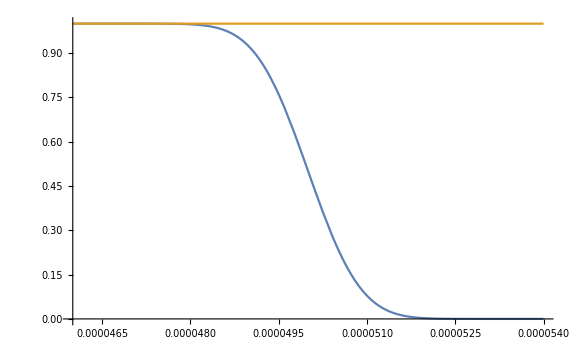

```mathematica
pulsesweep[t_,tl_,tk_]:=0.5*(Erfc[(t-tl)/(0.5*tk)])*(1-Erf[-t/(0.5*tk)+2 ])/2;
pulseArr=pulsesweep[t,#,tconst]&/@tsweepArr;
Plot[Evaluate[{pulseArr[[{#1,#2}]]}],{t,tminArr[[#1]],tmaxArr[[#1]]},PlotRange->Full,ImageSize->Large]&[5,-1]
```

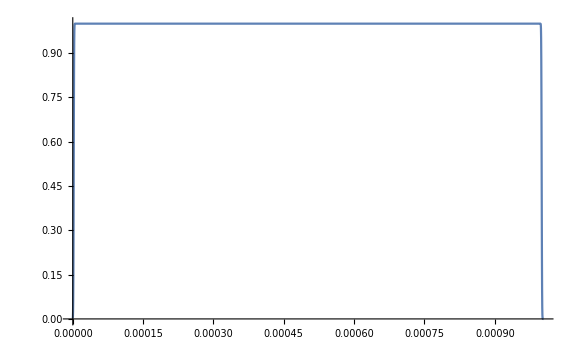

```mathematica
Plot[Evaluate[{pulseArr[[-1]]}],{t,0,tmaxArr[[-1]]},PlotRange->Full,ImageSize->Large]
```

### 0.7.3 Validity of Shortcut

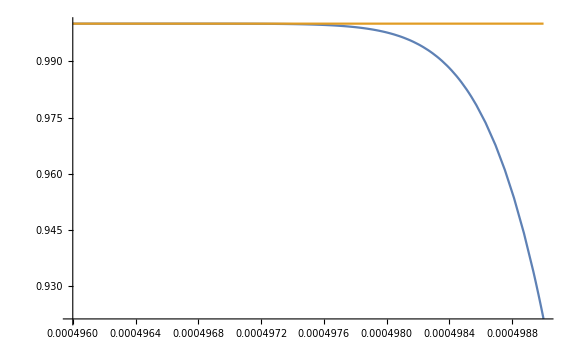

```mathematica
Plot[Evaluate[{pulseArr[[{#1,#2}]]}],{t,tminArr[[#1]],tminArr[[#1]]+3*μs},PlotRange->Full,ImageSize->Large]&[50,-1]
```

```mathematica
GetResids[func1_,func2_,t1_,t2_]:=NIntegrate[(func2-func1)^2,{t,t1,t2}];
(*GetResids[pulseArr[[#1]],pulseArr[[-1]],0,tminArr[[#1]]]&[1]
thde=GetResids[pulseArr[[#1]],pulseArr[[-1]],0,tminArr[[#1]]]&/@Range[3,Length[pulseArr]-1]*)
```

### 0.7.4 Eric’s Pulse

```mathematica
(*eric's pulses*)
tpulse=2.1875*^-6;
Pulse2[t_]:= 1/2(Erfc[(t-tswitch)/(0.5tpulse)]);
Pulse1[t_]:= (1-(Erfc[(t)/(0.5tpulse)])) ;
Pulse[t_] := Pulse1[t] *Pulse2[t];
```

```mathematica
(*eric's pulse timings*)
tsweepminEH=5*μs;tsweepmaxEH=200*μs;tsweepstepEH=2.5*μs;
tsweepArrEH=Range[tsweepminEH,tsweepmaxEH,tsweepstepEH];
pulseArrEH=Pulse[t]/.{tswitch->#}&/@tsweepArrEH;
tstopEH=0.000018873985580289792;
numPulsesEH=Length[tsweepArrEH]
```

79

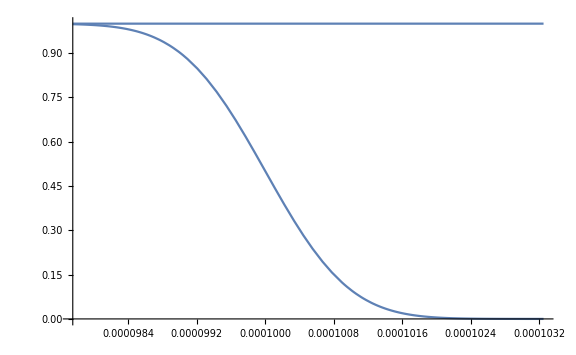

```mathematica
(*pulsing*)
tsweepbacksetEH=2.25*μs;tsweepoffsetEH=3.25*μs;
tminArrEH=tsweepArrEH-tsweepbacksetEH;tmaxArrEH=tsweepArrEH+tsweepoffsetEH;
tminArrEH=Clip[tminArrEH,{0,tsweepmaxEH}];

Plot[pulseArrEH[[{#1,#2}]],{t,tminArrEH[[#1]],tmaxArrEH[[#1]]},PlotRange->{0,1},ImageSize->Large]&[39,-1]
```

### 0.7.5 Create General Pulse Array

## 0.8 Composite Pulse Sequences

### 0.8.1 Pulse Sequencer

```mathematica
(*th1[state_,sequences_]=Module[{},

]*)
```

## 0.9 SiO+ Stuff

```mathematica
HE1RWA1SiO[Vm_,ΔDJ_,ion_]:=(ℏ*Ωm*Vm)/2*(σp[[ion]]*Exp[-I*ΔDJ*t]+σm[[ion]]*Exp[I*ΔDJ*t]);
HE2RWA1SiO[Vm_,xeq_,wm_,ΔDJ_,ion_,d_]:=ℏ*4*Ωm*Cos[wm*t]*Vm(#.Sum[η[[d,ion,activeModes[[d,i]]]]*(ah[[d,i]]),{i,numModes[[d]]}]+#*xeq/r0)&[Exp[-ⅈ*ΔDJ*t]*σp[[ion]]+Exp[ⅈ*ΔDJ*t]*σm[[ion]]];
```

```mathematica
GetSignificantStates[data_,threshold_:0.05]:=With[{ind=Flatten[Position[Max/@data,_?(#>threshold&)]]},
Basis[[(ind-1)*numPhononStates+1,;;numQubits]]]
```

## 0.10 Raman Stuff

```mathematica
HE2RWA1RAM[Vm_,xeq_,wm_,ΔDJ_,ion_,d_]:=ℏ*2*Ωm*Vm(#.Sum[η[[d,ion,activeModes[[d,i]]]]*(ah[[d,i]]),{i,numModes[[d]]}]+#*xeq/r0)&[Exp[-ⅈ*(ΔDJ+wm)*t]*σp[[ion]]+Exp[ⅈ*(ΔDJ+wm)*t]*σm[[ion]]];
```

```mathematica
ℏ*2*Ωm*Vm(#.Sum[η[[d,ion,activeModes[[d,i]]]]*(ah[[d,i]]),{i,numModes[[d]]}]+#*xeq/r0)&[Exp[-ⅈ*(ΔDJ+wm)*t]*σp[[ion]]+Exp[ⅈ*(ΔDJ+wm)*t]*σm[[ion]]]
```

Part::pkspec1: The expression ion cannot be used as a part specification.

Part::pkspec1: The expression 3.33564×10^-30 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

6.0648×10^-27 Vm ((ⅇ^(ⅈ t (wm+ΔDJ)) {SparseArray[…],SparseArray[…]}⟦ion⟧+ⅇ^(-ⅈ t (wm+ΔDJ)) {SparseArray[…],SparseArray[…]}⟦ion⟧).∑_i^({1,0}⟦3.33564×10^-30⟧) {{SparseArray[…]},{}}⟦3.33564×10^-30,i⟧ {{{0.0000143744,-0.0000154286},{0.0000143744,0.0000154286}},{{-0.0000155001,-0.0000203993},{0.0000155001,-0.0000203993}}}⟦3.33564×10^-30,ion,{{1},{}}⟦3.33564×10^-30,i⟧⟧+1818.18 xeq (ⅇ^(ⅈ t (wm+ΔDJ)) {SparseArray[…],SparseArray[…]}⟦ion⟧+ⅇ^(-ⅈ t (wm+ΔDJ)) {SparseArray[…],SparseArray[…]}⟦ion⟧))

### 0.10.1 Variables

```mathematica
(*ω0=Δ[[1,3]];
s1=1;s2=1;s3=1;
β=Δ[[1,4]]-Δ[[1,3]];*)
```

```mathematica
(*ΩR:=(Ωm^2*s1*s2*VmDJ1*VmDJ2)(2ΔDJ+δDJ)/(4ΔDJ(δDJ+ΔDJ));
Ωα:=(Ωm^2*s1*s2*VmDJ2^2)(2ΔDJ+2δDJ+ω0)/(4(ΔDJ+δDJ)(δDJ+ω0+ΔDJ));
Ωβ:=(Ωm^2*s1*s2*VmDJ1^2)(2ΔDJ+2δDJ+ω0)/(4ΔDJ(ΔDJ-ω0));
χu:=(Ωm*s2)^2/4*(VmDJ2^2/(ΔDJ+δDJ)+VmDJ1^2/(ΔDJ-ω0));
χd:=Ωm^2/4*((VmDJ2*s1)^2/(δDJ+ω0+ΔDJ)+(s1*VmDJ1)^2/ΔDJ+(s3*VmDJ2)^2/(δDJ+β+ω0+ΔDJ)+(s3*VmDJ1)^2/(ΔDJ+β));*)
```

```mathematica
(*{ΩR,Ωm}/wmhz
{χd,χu,χu-χd}/wmhz*)
```

## 0.11 Effective Hamiltonian (James & Jerke)

## 1 H_eff Creator

#### 6.1.1.1 General

```mathematica
(*ion parameters*)
xeqDJ=0;stateDJ=GroundState[{0,0}];
(*gate parameters*)
modeDJ=1;dirDJ=1;
```

```mathematica
(*trap hamiltonian*)
(*Hextrap=ToIntPic[Sum[HE2TRAP[xeqDJ,ωRF,qb,dirDJ],{qb,numIons}],UMT[[1]]]//N//Simplify;*)
Hextrap=0;
```

```mathematica
ΔDJ1=0*wmhz;ΔDJ2=ΔDJ1;
VmDJ1=10;VmDJ2=20;
δDJ=δIdeal[VmDJ1,{1,2},1,1]+wmvals[[dirDJ,modeDJ]];
tDJ=τIdeal[VmDJ1,{1,2},1,1];tDJ/μs
tDJ=1000*μs;
```

190.015

```mathematica
(*MS Raman*)
(*HexRE1R=ToIntPic[Sum[HE2RWA1RAM[VmDJ1,xeqDJ,0,Δ[[1,2]]-Δ[[1,1]]-ΔDJ1,ion,dirDJ],{ion,numQubits}],UMT[[1]]];
HexRE1B=ToIntPic[Sum[HE2RWA1RAM[VmDJ1,xeqDJ,0,Δ[[1,4]]-Δ[[1,1]]-ΔDJ2,ion,dirDJ],{ion,numQubits}],UMT[[1]]];
HexRE2R=ToIntPic[Sum[HE2RWA1RAM[VmDJ2,xeqDJ,δDJ,Δ[[1,2]]-Δ[[1,3]]-ΔDJ1,ion,dirDJ],{ion,numQubits}],UMT[[1]]];
HexRE2B=ToIntPic[Sum[HE2RWA1RAM[VmDJ2,xeqDJ,-δDJ,Δ[[1,4]]-Δ[[1,3]]-ΔDJ2,ion,dirDJ],{ion,numQubits}],UMT[[1]]];
HexRETOT=HexRE1R+HexRE1B+HexRE2R+HexRE2B;*)
HexRETOT=ToIntPic[Sum[HE2RWA1RAM[VmDJ1,xeqDJ,δDJ,Δ[[1,2]]-Δ[[1,1]],ion,dirDJ],{ion,numQubits}],UMT[[1]]]+ToIntPic[Sum[HE2RWA1RAM[VmDJ1,xeqDJ,-δDJ,Δ[[1,2]]-Δ[[1,1]],ion,dirDJ],{ion,numQubits}],UMT[[1]]];
```

## 1.1 Setup

```mathematica
Commutator[m1_,m2_]:=m1.m2-m2.m1;
```

```mathematica
HexDJ=HexRETOT;
```

```mathematica
Heff[Ham_]:=Module[{arrayrules=Expand[ArrayRules[SparseArray[Ham]][[;;-2]]],arraydim=Dimensions[Ham],
ind, expr, vals, coefficientsArr,exponentsArr,uniqueExponents,coefficientsArrPositions,hcoeffArr,hcoeffPos,hMatArr,Heff},
(*split index from values and get each element of sum separately*)
ind=arrayrules[[;;,1]];expr=arrayrules[[;;,2]]/.{x_+0.:>x};vals=List@@@expr;
(*separate coefficients from exponent*)
coefficientsArr=vals/.{x_*ⅇ^(__):>x};
exponentsArr=Exponent[#,ⅇ]&/@vals;
(*then strip zeros and t from exponent*)
exponentsArr=Re[exponentsArr/.{t->-ⅈ}];
(*make exponent same precision as later exp*)
exponentsArr=SetPrecision[exponentsArr,9];
(*get unique exponents*)
uniqueExponents=DeleteDuplicates[Flatten[exponentsArr]]//Sort;
(*get coefficient positions for each unique exponent*)
coefficientsArrPositions=Position[exponentsArr,#]&/@uniqueExponents;
(*get coefficients*)
hcoeffArr=Apply[coefficientsArr[[##]]&,coefficientsArrPositions,{2}];
(*get positions*)
hcoeffPos=ind[[#,;;]]&/@coefficientsArrPositions[[;;,;;,1]];
(*create matrix for each unique exponent*)
hMatArr=MapThread[SparseArray[#1->#2,arraydim]&,{hcoeffPos,hcoeffArr}];
(*do effective hamiltonian for each one*)
Heff=Commutator[hMatArr[[#]],hMatArr[[-#]]]&/@Range[Length[hMatArr]/2];
uniqueExponents=#[[;;Length[#]/2]]&[uniqueExponents];
Return[AssociationThread[uniqueExponents->Heff]]
]
```

## 1.2 Trial

```mathematica
(8*(10*Ωm)^2*η[[1,1,1]]*η[[1,1,2]])/δIdeal[VmDJ1,{1,2},1,1]
```

-4436.47

```mathematica
res1=Heff[HexDJ];
res2=1/ℏ*Values[res1]/Keys[res1];
res3=Total[res2];
```

```mathematica
res3/ℏ//MatrixForm
```

(4122.47 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4123.15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 4121.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4123.15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 4119.74 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4123.15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -12371.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -12369.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 4123.56 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4123.15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 4124.34 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4123.15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 4125.11 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4123.15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -12368.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -12369.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2066.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2074.02 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2081.55 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -6176.92 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2057.88 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00267902 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2048.22 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00267902 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2038.55 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00267902 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -6202.62 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00803705 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 4123.15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4123.56 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 4123.15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4124.34 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 4123.15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4125.11 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -12369.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -12368.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4123.15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4124.66 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 4123.15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4127.57 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 4123.15 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4130.49 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -12369.4 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -12365.2 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2067.59 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0574209 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2077.26 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0574209 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2086.92 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0574209 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -6173.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.172263 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2058.97 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2051.45 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2043.93 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -6199.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2066.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2074.02 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2081.55 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -6176.92 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0574209 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2067.59 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0574209 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2077.26 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0574209 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2086.92 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.172263 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -6173.8 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 10.5286 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 26.9391 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 43.3496 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 17.6459 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.90843 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.26587 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.13344 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.26587 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.358452 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.26587 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -8.05024 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -6.79761 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00267902 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2057.88 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00267902 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2048.22 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00267902 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2038.55 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.00803705 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -6202.62 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2058.97 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2051.45 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2043.93 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -6199.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.26587 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.90843 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.26587 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.13344 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.26587 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.358452 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -6.79761 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -8.05024 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -6.71171 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -24.6722 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -42.6327 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -33.7464)